## Actividad “Todo Terreno”

## Mario Jacob García Navarro - A01363206

## Métodos

### Método de Bisección

```mathematica
Biseccion[a0_,b0_,m_] :=
Module[{},
a = N[a0];  
b = N[b0];  
c = (a + b)/2; 
k = 0; 
output={{k,a,c,b,f[c]}}; 
While[k < m,
If[ Sign[f[b]] ==  Sign[f[c]], 
b = c, a = c; ]; 
c = (a + b)/2; 
k = k+1; 
output=Append[output,{k,a,c,b,f[c]}]; ]; 
Print[NumberForm[TableForm[output,
TableHeadings->{None,{"k","a_k","c_k","b_k","f[c_k]"}}],16]]; 
Print["  c  = ",NumberForm[c,16] ]; 
Print[" Δc  = ±",(b-a)/2]; 
Print["f[c] = ",NumberForm[f[c],16] ]; ]
```

### Método de la Secante

```mathematica
Secante[x0_,x1_,max_]:=
Module[{},
k = 1; 
p0 = N[x0]; 
p1 = N[x1]; 
Print["f[x] = ",f[x] ];
Print["p_(k + 1) = g[p_k,p_(k - 1)] = p_k - (f[SubscriptBox[p, k]] (SubscriptBox[p, k] - SubscriptBox[p, k - 1]))/(f[SubscriptBox[p, k]] - f[SubscriptBox[p, k - 1]])"]; 
Print["p_0 = ",PaddedForm[p0,{16,16}],",   f[p_0] = ",NumberForm[f[p0],16] ]; 
Print["p_1 = ",PaddedForm[p1,{16,16}],",   f[p_1] = ",NumberForm[f[p1],16] ];  
p2 = p1; 
p1 = p0; 
While[ k<max,
p0 = p1; 
p1 = p2; 
p2 = p1 - (f[p1](p1 - p0))/(f[p1] - f[p0]); 
k = k+1; 
Print[Subscript["p", k]," = ",PaddedForm[p2,{16,16}],",   f[",Subscript["p", k],"] = ",NumberForm[f[p2],16] ]; ]; 
Print[""]; 
Print["f[x] = ",f[x] ];
Print["  p  = ",NumberForm[p2,16] ]; 
Print[" Δp  = ±",Abs[p2-p1] ]; 
Print["f[p] = ",NumberForm[f[p2],16] ]; ]
```

### Método de Newton-Raphson

```mathematica
NewtonRaphson[x0_,max_]:=
Module[{},
k = 0; 
p0 = N[x0]; 
Print["f[x] = ",f[x] ];
g[x_]=x-f[x]/f'[x]; 
Print["g[x] = x - f[x]/f'[x]"]; 
Print["g[x] = ",g[x] ];
Print["g[x] = ",Simplify[g[x]]];
Print["  p_0 = ",PaddedForm[p0,{16,16}],",   f[p_0] = ",NumberForm[f[p0],16] ]; 
p1 = p0; 
While[ k<max,
p0 = p1; 
p1 = p0 - f[p0]/f'[p0]; 
k = k+1;  
Print[Subscript["  p", k]," = ",PaddedForm[p1,{16,16}],",   f[",Subscript["p", k],"] = ",NumberForm[f[p1],16] ]; ]; 
Print[""]; 
Print["f[x] = ",f[x] ];
Print["  p  = ",NumberForm[p1,16] ]; 
Print[" Δp  = ±",Abs[p1-p0] ]; 
Print["f[p] = ",NumberForm[f[p1],16] ]; ]
```

## Inciso a)

```mathematica
l=89; h=49; d=55; β=0.200712864;
```

```mathematica
A=l Sin[ β]; B=l Cos[ β];c1=(h+0.5 d) Sin[ β]-0.5 d Tan[ β];e=(h+0.5 d) Cos[ β]-0.5 d;
```

```mathematica
f[α_]:=A Sin[α] Cos[α]+B (Sin[α])^2-c1 Cos[α]-e Sin[α]
```

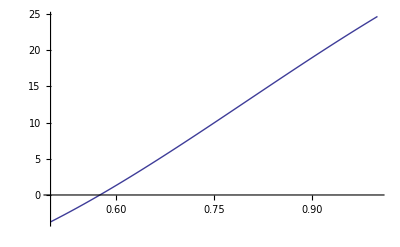

```mathematica
Plot[f[x],{x,0.5,1}]
```

```mathematica
NewtonRaphson[0.5,4]
```

f[x] = -9.65671 Cos[x]-47.4642 Sin[x]+17.7437 Cos[x] Sin[x]+87.2133 Sin[x]^2

g[x] = x - f[x]/f'[x]

g[x] = x-(-9.65671 Cos[x]-47.4642 Sin[x]+17.7437 Cos[x] Sin[x]+87.2133 Sin[x]^2)/(-47.4642 Cos[x]+17.7437 Cos[x]^2+9.65671 Sin[x]+174.427 Cos[x] Sin[x]-17.7437 Sin[x]^2)

g[x] = x+(Cos[x] (0.544232-1. Sin[x])+(2.67498-4.91516 Sin[x]) Sin[x])/(1. Cos[x]^2+(0.544232-1. Sin[x]) Sin[x]+Cos[x] (-2.67498+9.83031 Sin[x]))

p_0 =  0.5000000000000000,   f[p_0] = -3.71882804672217

p_1 =  0.5809314748523632,   f[p_1] = 0.2865929419691611

p_2 =  0.5754932208137343,   f[p_2] = 0.00105708070262267

p_3 =  0.5754730124763138,   f[p_3] = 1.482892741933028×10^-8

p_4 =  0.5754730121928194,   f[p_4] = 0.

f[x] = -9.65671 Cos[x]-47.4642 Sin[x]+17.7437 Cos[x] Sin[x]+87.2133 Sin[x]^2

p  = 0.5754730121928194

Δp  = ±2.83494×10^-10

f[p] = 0.

```mathematica
Biseccion[0,1,10]
```

k | a_k | c_k | b_k | f[c_k]
0 | 0. | 0.5 | 1. | -3.71882804672217
1 | 0.5 | 0.75 | 1. | 9.95251399230238
2 | 0.5 | 0.625 | 0.75 | 2.673336783309651
3 | 0.5 | 0.5625 | 0.625 | -0.6723627926761324
4 | 0.5625 | 0.59375 | 0.625 | 0.967837987634773
5 | 0.5625 | 0.578125 | 0.59375 | 0.1389737272792004
6 | 0.5625 | 0.5703125 | 0.578125 | -0.2689601338224605
7 | 0.5703125 | 0.57421875 | 0.578125 | -0.06555030175557874
8 | 0.57421875 | 0.576171875 | 0.578125 | 0.03657360332361037
9 | 0.57421875 | 0.5751953125 | 0.576171875 | -0.01452302233118274
10 | 0.5751953125 | 0.57568359375 | 0.576171875 | 0.01101664043017792

c  = 0.57568359375

Δc  = ±0.000488281

f[c] = 0.01101664043017792

```mathematica
Secante[0,1,9]
```

f[x] = -9.65671 Cos[x]-47.4642 Sin[x]+17.7437 Cos[x] Sin[x]+87.2133 Sin[x]^2

p_(k + 1) = g[p_k,p_(k - 1)] = p_k - (f[SubscriptBox[p, k]] (SubscriptBox[p, k] - SubscriptBox[p, k - 1]))/(f[SubscriptBox[p, k]] - f[SubscriptBox[p, k - 1]])

p_0 =  0.0000000000000000,   f[p_0] = -9.65670874972058

p_1 =  1.0000000000000000,   f[p_1] = 24.66326720308537

p_2 =  0.2813728297187534,   f[p_2] = -10.99891362296383

p_3 =  0.5030114953851235,   f[p_3] = -3.580016625156329

p_4 =  0.6099640663801869,   f[p_4] = 1.84519642377564

p_5 =  0.5735878909685038,   f[p_5] = -0.0984769012622948

p_6 =  0.5754309028512986,   f[p_6] = -0.002202577142199402

p_7 =  0.5754730675289834,   f[p_7] = 2.894505911399392×10^-6

p_8 =  0.5754730121912016,   f[p_8] = -8.46256398290279×10^-11

p_9 =  0.5754730121928194,   f[p_9] = 0.

f[x] = -9.65671 Cos[x]-47.4642 Sin[x]+17.7437 Cos[x] Sin[x]+87.2133 Sin[x]^2

p  = 0.5754730121928194

Δp  = ±1.61782×10^-12

f[p] = 0.

Como se puede observar, el resultado que satisface a la ecuación resulta ser “ 0.5754730121928194” radianes, lo que sería aproximadamente 32.97°. Se puede concluir que el ángulo de 33° es una muy buena aproximación.

## Inciso b)

```mathematica
Clear[f]
```

```mathematica
l=89; h=49; d1=30; β=0.200712864;
```

```mathematica
A=l Sin[ β]; B=l Cos[ β];c1=(h+0.5 d1) Sin[ β]-0.5 d1 Tan[ β];e=(h+0.5 d1) Cos[ β]-0.5 d1;
```

```mathematica
f[α_]:=A Sin[α] Cos[α]+B (Sin[α])^2-c1 Cos[α]-e Sin[α]
```

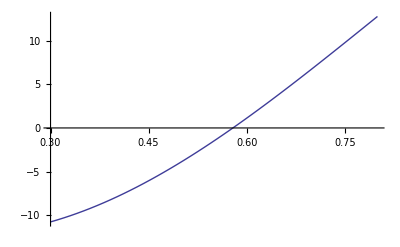

```mathematica
Plot[f[x],{x,0.3,0.8}]
```

```mathematica
NewtonRaphson[0.7,5]
```

f[x] = -9.70776 Cos[x]-47.7152 Sin[x]+17.7437 Cos[x] Sin[x]+87.2133 Sin[x]^2

g[x] = x - f[x]/f'[x]

g[x] = x-(-9.70776 Cos[x]-47.7152 Sin[x]+17.7437 Cos[x] Sin[x]+87.2133 Sin[x]^2)/(-47.7152 Cos[x]+17.7437 Cos[x]^2+9.70776 Sin[x]+174.427 Cos[x] Sin[x]-17.7437 Sin[x]^2)

g[x] = x+(Cos[x] (0.547109-1. Sin[x])+(2.68913-4.91516 Sin[x]) Sin[x])/(1. Cos[x]^2+(0.547109-1. Sin[x]) Sin[x]+Cos[x] (-2.68913+9.83031 Sin[x]))

p_0 =  0.7000000000000000,   f[p_0] = 6.773866149769944

p_1 =  0.5846402713039978,   f[p_1] = 0.3014602579888574

p_2 =  0.5789285478056443,   f[p_2] = 0.001150489555875822

p_3 =  0.5789065812719611,   f[p_3] = 1.730534648913817×10^-8

p_4 =  0.5789065809415366,   f[p_4] = 7.105427357601002×10^-15

p_5 =  0.5789065809415365,   f[p_5] = 0.

f[x] = -9.70776 Cos[x]-47.7152 Sin[x]+17.7437 Cos[x] Sin[x]+87.2133 Sin[x]^2

p  = 0.5789065809415365

Δp  = ±1.11022×10^-16

f[p] = 0.

```mathematica
Biseccion[0.6,0.8,10]
```

k | a_k | c_k | b_k | f[c_k]
0 | 0.6 | 0.7 | 0.8 | 6.773866149769944
1 | 0.6 | 0.6499999999999999 | 0.7 | 3.885715621915281
2 | 0.6 | 0.625 | 0.6499999999999999 | 2.485108408682947
3 | 0.6 | 0.6125 | 0.625 | 1.797876971629265
4 | 0.6 | 0.60625 | 0.6125 | 1.457802896551108
5 | 0.6 | 0.6031249999999999 | 0.60625 | 1.288685308743354
6 | 0.6 | 0.6015625 | 0.6031249999999999 | 1.204360621008298
7 | 0.6 | 0.60078125 | 0.6015625 | 1.162257333422282
8 | 0.6 | 0.600390625 | 0.60078125 | 1.141220519870565
9 | 0.6 | 0.6001953124999999 | 0.600390625 | 1.130705828923453
10 | 0.6 | 0.60009765625 | 0.6001953124999999 | 1.125449413440464

c  = 0.60009765625

Δc  = ±0.0000976562

f[c] = 1.125449413440464

```mathematica
Secante[0.6,0.8,7]
```

f[x] = -9.70776 Cos[x]-47.7152 Sin[x]+17.7437 Cos[x] Sin[x]+87.2133 Sin[x]^2

p_(k + 1) = g[p_k,p_(k - 1)] = p_k - (f[SubscriptBox[p, k]] (SubscriptBox[p, k] - SubscriptBox[p, k - 1]))/(f[SubscriptBox[p, k]] - f[SubscriptBox[p, k - 1]])

p_0 =  0.6000000000000000,   f[p_0] = 1.120193618344793

p_1 =  0.8000000000000000,   f[p_1] = 12.75579320889489

p_2 =  0.5807454079245806,   f[p_2] = 0.0964259748394838

p_3 =  0.5790753530641741,   f[p_3] = 0.0088401366147508

p_4 =  0.5789067925591956,   f[p_4] = 0.00001108306940267312

p_5 =  0.5789065809659863,   f[p_5] = 1.280511696677422×10^-9

p_6 =  0.5789065809415365,   f[p_6] = 0.

p_7 =  0.5789065809415365,   f[p_7] = 0.

f[x] = -9.70776 Cos[x]-47.7152 Sin[x]+17.7437 Cos[x] Sin[x]+87.2133 Sin[x]^2

p  = 0.5789065809415365

Δp  = ±0.

f[p] = 0.

El valor de α es: 0.5789065809415365 radianes ≃ 33.1689038 grados